```mathematica
f=Function[{t, α, β}, β^α/Gamma[α] * t^(α-1)*E^(-β*t)]
```

Function[{t,α,β},(β^α t^(α-1) ⅇ^(-β t))/Gamma[α]]

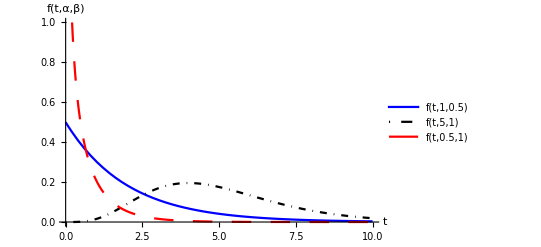

```mathematica
Plot[{f[t,1,0.5], f[t,5,1], f[t,0.5,1]}, {t, 0, 10},
PlotRange->{0,1},
PlotStyle->
{{Thick, Blue}, 
{DotDashed, Thick, Black},
 {Dashing[Large], Red}},
PlotLegends->"Expressions",
AxesLabel->{"t","f(t,α,β)"},
AxesStyle->Gray]
```

```mathematica
F=Function[{t,α,β}, Integrate[f[x,α,β],{x,0,t}]]
```

Function[{t,α,β},∫_0^t f[x,α,β]ⅆx]

```mathematica
Plot[{F[t, 1,0.5], F[t,5,1], F[t,0.5,1]}, {t, 0,15},
PlotRange->{0,1},
Ticks->{Range[0,15,1], Range[0,1,0.1]},
PlotStyle->
{{Thick, Blue}, 
{DotDashed, Thick, Black},
 {Dashing[Large], Red}},
PlotLegends->"Expressions",
AxesLabel->{"t","f(t,α,β)"},
AxesStyle->Gray]
```

$Aborted

```mathematica
M[α_,β_]:=α/β
an[α_,β_,n_]:=NIntegrate[t^n*f[t,α,β], {t, 0, Infinity}]
a1[α_,β_]:=an[α,β,1]
a2[α_,β_]:=an[α,β,2]
a3[α_,β_]:=an[α,β,3]
Disp[α_,β_]:=a2[α,β]-(a1[α,β])^2
σ[α_,β_]:=Sqrt[Disp[α,β]]
```

```mathematica
Disp[1,0.5]
Disp[5,1]
Disp[0.5,1]
```

4.

5.

0.5

```mathematica
σ[1,0.5]
σ[5,1]
σ[0.5,1]
```

2. σ(1, 0.5) =

2.23607

0.707107

```mathematica
M[1,0.5]
M[5,1]
M[0.5,1]
```

2.

5

0.5

```mathematica
R=RandomVariate[GammaDistribution[1,0.5], 10]
```

{1.84495,0.27607,0.744699,0.500946,0.760128,0.931384,0.163377,0.552313,0.982196,0.223101}

```mathematica
R
maxR=Max[R]+0.1
R=Map[Function[x,x/maxR], R]
```

{1.,0.149635,0.403642,0.271523,0.412005,0.504829,0.0885535,0.299365,0.53237,0.120925}

1.1

{0.909091,0.136032,0.366947,0.246839,0.37455,0.458936,0.0805032,0.27215,0.483973,0.109932}

```mathematica
X=Map[Function[x,SolveAlways[F[t,1,0.5]==x,t]],R]
```

{{{t→4.79579}},{{t→0.29244}},{{t→0.914404}},{{t→0.566953}},{{t→0.938568}},{{t→1.22844}},{{t→0.167857}},{{t→0.63532}},{{t→1.32319}},{{t→0.232915}}}

```mathematica
G={t,0}/.Map[Function[x,Indexed[x,1]], X]
```

{{4.79579,0},{0.29244,0},{0.914404,0},{0.566953,0},{0.938568,0},{1.22844,0},{0.167857,0},{0.63532,0},{1.32319,0},{0.232915,0}}

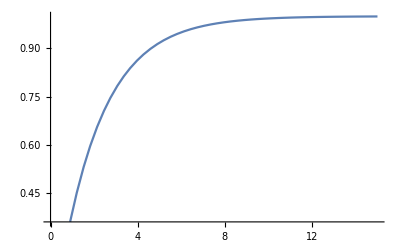

```mathematica
Plot[F[t,1,0.5], {t,0,15},Epilog->{Red,Point[G]}]
```